```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPAp_mub0/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub0/buffer/Zphi.dat"]];
T0=Flatten[Import["./LPAp_mub0/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./LPAp_mub300/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub300/buffer/Zphi.dat"]];
T300=Flatten[Import["./LPAp_mub300/buffer/TMeV.dat"]];
t=(T300-T300[[1]])/T300[[1]];
datamub300=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub300=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
b1mub300linear=Transpose[{T300[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];

fpi=Flatten[Import["./LPAp_mub400/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub400/buffer/Zphi.dat"]];
T400=Flatten[Import["./LPAp_mub400/buffer/TMeV.dat"]];
t=(T400-T400[[1]])/T400[[1]];
datamub400=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub400=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
b1mub400linear=Transpose[{T400[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];

fpi=Flatten[Import["./LPAp_mub500/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub500/buffer/Zphi.dat"]];
T500=Flatten[Import["./LPAp_mub500/buffer/TMeV.dat"]];
t=(T500-T500[[1]])/T500[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub500=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
b1mub500linear=Transpose[{T500[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];

fpi=Flatten[Import["./LPAp_mub600/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub600/buffer/Zphi.dat"]];
T600=Flatten[Import["./LPAp_mub600/buffer/TMeV.dat"]];
t=(T600-T600[[1]])/T600[[1]];
datamub600=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub600=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
b1mub600linear=Transpose[{T600[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
```

## Plot

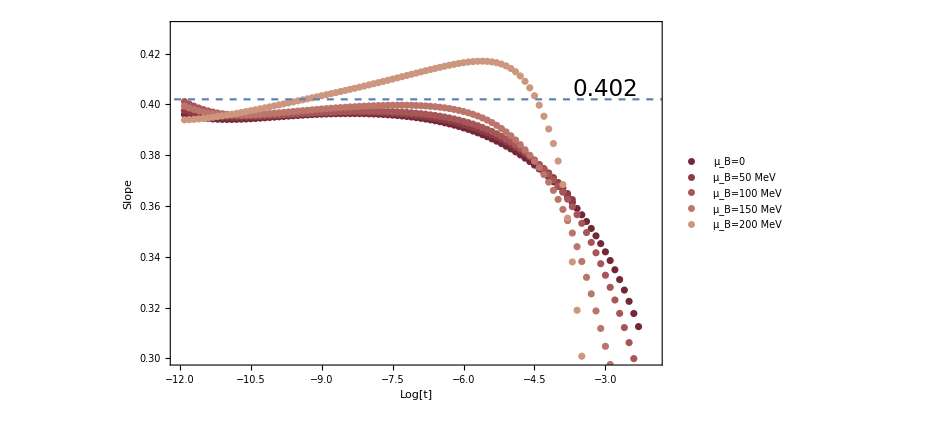

```mathematica
plotT=Show[ListPlot[{b1mub0,b1mub300,b1mub400,b1mub500,b1mub600},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["Slope",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.0714}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=50 MeV","μ_B=100 MeV","μ_B=150 MeV","μ_B=200 MeV","μ_B=250 MeV","μ_B=300 MeV","μ_B=350 MeV","μ_B=400 MeV","μ_B=450 MeV","μ_B=500 MeV","μ_B=550 MeV","μ_B=600 MeV","μ_B=650 MeV","μ_B=700 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},{0.3,0.43}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.402},{10,0.402}},PlotStyle->Dashed],ImageSize->700,Background->None,Epilog->{Text[Style["0.402",23],{-3,0.406}]}]
```

```mathematica
muball={0,300,400,500,600};
dataall={b1mub0,b1mub300,b1mub400,b1mub500,b1mub600};
lineardataall={b1mub0linear,b1mub300linear,b1mub400linear,b1mub500linear,b1mub600linear};
```

```mathematica
(*Export["Tscaling.pdf",plotT];*)
```

```mathematica
Table[Export["./LOdata/mub"<>ToString[muball[[i]]]<>".dat",dataall[[i]]],{i,1,Length[muball]}]
```

{./LOdata/mub0.dat,./LOdata/mub300.dat,./LOdata/mub400.dat,./LOdata/mub500.dat,./LOdata/mub600.dat}

```mathematica
Export["./LOdata/t.dat",t]
```

./LOdata/t.dat

```mathematica
Length[t]
```

100

```mathematica
Length[b1mub0]
```

97

# plot on phase diagram

## data

```mathematica
mub0data=Table[{0,Transpose[b1mub0linear][[1]][[i]],Transpose[b1mub0linear][[2]][[i]]},{i,1,Length[b1mub0linear]}];
mub50data=Table[{50,Transpose[b1mub50linear][[1]][[i]],Transpose[b1mub50linear][[2]][[i]]},{i,1,Length[b1mub50linear]}];
mub100data=Table[{100,Transpose[b1mub100linear][[1]][[i]],Transpose[b1mub100linear][[2]][[i]]},{i,1,Length[b1mub100linear]}];
mub150data=Table[{150,Transpose[b1mub150linear][[1]][[i]],Transpose[b1mub150linear][[2]][[i]]},{i,1,Length[b1mub150linear]}];
mub200data=Table[{200,Transpose[b1mub200linear][[1]][[i]],Transpose[b1mub200linear][[2]][[i]]},{i,1,Length[b1mub200linear]}];
mub250data=Table[{250,Transpose[b1mub250linear][[1]][[i]],Transpose[b1mub250linear][[2]][[i]]},{i,1,Length[b1mub250linear]}];
mub300data=Table[{300,Transpose[b1mub300linear][[1]][[i]],Transpose[b1mub300linear][[2]][[i]]},{i,1,Length[b1mub300linear]}];
mub350data=Table[{350,Transpose[b1mub350linear][[1]][[i]],Transpose[b1mub350linear][[2]][[i]]},{i,1,Length[b1mub350linear]}];
mub400data=Table[{400,Transpose[b1mub400linear][[1]][[i]],Transpose[b1mub400linear][[2]][[i]]},{i,1,Length[b1mub400linear]}];
mub450data=Table[{450,Transpose[b1mub450linear][[1]][[i]],Transpose[b1mub450linear][[2]][[i]]},{i,1,Length[b1mub450linear]}];
mub500data=Table[{500,Transpose[b1mub500linear][[1]][[i]],Transpose[b1mub500linear][[2]][[i]]},{i,1,Length[b1mub500linear]}];
mub550data=Table[{550,Transpose[b1mub550linear][[1]][[i]],Transpose[b1mub550linear][[2]][[i]]},{i,1,Length[b1mub550linear]}];
mub575data=Table[{575,Transpose[b1mub575linear][[1]][[i]],Transpose[b1mub575linear][[2]][[i]]},{i,1,Length[b1mub575linear]}];
mub600data=Table[{600,Transpose[b1mub600linear][[1]][[i]],Transpose[b1mub600linear][[2]][[i]]},{i,1,Length[b1mub600linear]}];
mub625data=Table[{625,Transpose[b1mub625linear][[1]][[i]],Transpose[b1mub625linear][[2]][[i]]},{i,1,Length[b1mub625linear]}];
mub650data=Table[{650,Transpose[b1mub650linear][[1]][[i]],Transpose[b1mub650linear][[2]][[i]]},{i,1,Length[b1mub650linear]}];
mub675data=Table[{675,Transpose[b1mub675linear][[1]][[i]],Transpose[b1mub675linear][[2]][[i]]},{i,1,Length[b1mub675linear]}];
mub700data=Table[{700,Transpose[b1mub700linear][[1]][[i]],Transpose[b1mub700linear][[2]][[i]]},{i,1,Length[b1mub700linear]}];
```

Part::partw: Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]] 的部分 2 不存在.

```mathematica
mumub100data=Table[{Transpose[mub100linear][[1]][[i]],131.1413090,Transpose[mub100linear][[2]][[i]]},{i,1,Length[mub100linear]}];
mumub200data=Table[{Transpose[mub200linear][[1]][[i]],128.063591,Transpose[mub200linear][[2]][[i]]},{i,1,Length[mub200linear]}];
mumub300data=Table[{Transpose[mub300linear][[1]][[i]],122.759313,Transpose[mub300linear][[2]][[i]]},{i,1,Length[mub300linear]}];
mumub400data=Table[{Transpose[mub400linear][[1]][[i]],114.915769,Transpose[mub400linear][[2]][[i]]},{i,1,Length[mub400linear]}];
mumub500data=Table[{Transpose[mub500linear][[1]][[i]],103.947155,Transpose[mub500linear][[2]][[i]]},{i,1,Length[mub500linear]}];
mumub600data=Table[{Transpose[mub600linear][[1]][[i]],88.6153476,Transpose[mub600linear][[2]][[i]]},{i,1,Length[mub600linear]}];
mumub650data=Table[{Transpose[mub650linear][[1]][[i]],78.395755,Transpose[mub650linear][[2]][[i]]},{i,1,Length[mub650linear]}];
mumub700data=Table[{Transpose[mub700linear][[1]][[i]],64.8265550,Transpose[mub700linear][[2]][[i]]},{i,1,Length[mub700linear]}];
```

## Plot

```mathematica
(*ListContourPlot[Flatten[{mumub100data,mumub200data,mumub300data,mumub400data,mumub500data,mumub600data,mumub650data,mumub700data},1],Contours->{0.35,0.36,0.37,0.38,0.39,0.4}],*)
plot=ListContourPlot[Flatten[{mub0data,mub50data,mub100data,mub150data,mub200data,mub250data,mub300data,mub350data,mub400data,mub450data,mub500data,mub550data,mub575data,mub600data,mub625data,mub650data,mub675data,mub700data},1],Contours->{0.34,0.35,0.36,0.37,0.38,0.39,0.4},PlotRange->{{0,800},{50,135}}]
```

ListContourPlot::arrayerr: {{0.,103.934,0.396039},{0.,103.934,0.395602},{0.,103.934,0.395224},{0.,103.934,0.394905},{0.,103.934,0.394645},{0.,103.934,0.394439},{0.,103.934,0.394286},{0.,103.934,0.394179},{0.,103.933,0.394116},{0.,103.933,0.39409},«474»} 必须是一个有效数组.

ListContourPlot[{{0,103.93427653920122400581476352753062,0.396039074384043295570475003268},{0,103.93420231371061612703847685476262,0.395601801512416842752259798286},{0,103.9341202818570164022911904262317,0.395223647348894068160406898662},{0,103.93402962263806214737280084508145,0.394905079817434159077858825633},{0,103.93392942870581845231005704265317,0.394644608442799239518645976462},{0,103.93381869728573507860485762620524,0.394439446323682444014825789245},{0,103.93369632014054171628162399109341,0.394285830267830001052238367376},{0,103.93356107247863689121498414648151,0.394179448958897913465002251829},{0,103.93341160069596195090307194132031,0.394115687339534500028734768763},{0,103.93324640882867668343762499219212,0.394089819168700244772746079368},{0,103.93306384358105039385256311279829,0.3940971942476135223897902280586},{0,103.93286207777872253944355034637443,0.3941332948557309335557301979528},{0,103.93263909208172759494565702909613,0.3941938328356221935096579439758},{0,103.93239265477426195395521657184688,0.3942748022333022023859361822546},{0,103.9321202994289220608513782941906,0.3943724952048096377732275624599},{0,103.93181930022186996113280774019857,0.394483489789972198815565583415},{0,103.93148664465187215013792388059537,0.3946046861105979947985938620736},{0,103.93111900339017469149896687295765,0.39473328165788905459660241373},{0,103.93071269695946202170845353402183,0.3948667395893628689410057697453},{0,103.93026365890841126092541190333275,0.3950027978852542611705521628573},{0,103.92976739511328059210420731705483,0.3951394283630009412181865666084},{0,103.92921893879920832573574098749989,0.3952748291467792501428615224838},{0,103.92861280083106069337748997681587,0.3954074030819057150721112231887},{0,103.92794291477632246686699663946198,0.3955357330132140783856959296431},{0,103.92720257619020134753576734865471,0.3956585636817833180631966016148},{0,103.92638437551529104316968860658651,0.3957747824462953656877199937866},{0,103.92548012392423030758809365432486,0.3958834013012547600922545269157},{0,103.92448077136316634936653114464965,0.3959835373278087697942944548616},{0,103.92337631597577404495449927279078,0.3960744059111009010323140997614},{0,103.92215570400131609683455183625665,0.3961552970970515105430759655642},{0,103.92080671914489027736174868095451,0.3962255600429011816007301526648},{0,103.91931586031264400875579296583481,0.3962846009774677503712185288236},{0,103.91766820648828921214888532130338,0.3963318648001929288952383210864},{0,103.91584726739855616972680154745447,0.396366822683366112517998698459},{0,103.91383481847299606914118918167275,0.396388961287050101889977407755},{0,103.91161071844635446213154213076783,0.3963977801016018412031629550307},{0,103.90915270777801888497133617099489,0.39639277793040635567958597397132},{0,103.90643618587105471896031009241964,0.39637344407350684524136445024097},{0,103.90343396486116252258678919273411,0.39633924992732575188154608904745},{0,103.90011599751139396595107067769408,0.39628964538704225897244609805606},{0,103.89644907648930522677722586651244,0.3962240506392416830528496859744},{0,103.89239650201681252276131210182088,0.39614184695369524127663064977776},{0,103.88791771456647782768252576705498,0.39604237392808353727993991834085},{0,103.88296788892812574368239908662181,0.39592492231276132368087929096356},{0,103.8774974855830737924479925404507,0.39578872759982554362015528345242},{0,103.87145175489597863372475702315689,0.39563296574015986956468972919751},{0,103.86477018916208356123851311544421,0.3954567484315899286733722746728},{0,103.85738591702577195568542193588716,0.39525911727025942927181979774113},{0,103.8492250342095640347941830106687,0.39503903907091110159277952461895},{0,103.8402058638552677501825282991693,0.39479540186538407507984916170241},{0,103.83023813907452946125920190487456,0.39452701125435796289042373214539},{0,103.8192220995274755430676203893385,0.39423258556195200421491542610979},{0,103.80704749298770032287776687531333,0.39391075257372037555766335060928},{0,103.7935924719009271591991432526184,0.39356004550634207478691495925148},{0,103.77872237389373086385166869296717,0.39317890035131679457744682120095},{0,103.76228837402724287592133939531802,0.3927656537404442627650233307072},{0,103.74412599530714127580834870556919,0.39231854096190222165457361019068},{0,103.72405346254260898454709948921208,0.39183569611622939912817376510409},{0,103.70186988307912731494566926369627,0.39131515451747326599180470579999},{0,103.67735323619726719557984975910703,0.39075485844174376813401881064598},{0,103.65025815105470538380777735851416,0.39015266673464391619977375736998},{0,103.62031345093236250658478710178515,0.38950637072413942789362382475671},{0,103.58721943920665287121353957362442,0.38881371627480068441581907492532},{0,103.55064489988494410590631193016436,0.388072431561064016916979766100801},{0,103.51022378268457735539480692387345,0.387280260446369897210263107464039},{0,103.46555153947860468228688655271751,0.386434996366310446092767412900613},{0,103.41618107544216125097174949828949,0.385534511153691801521212990577123},{0,103.36161827437718432018992074550623,0.384576770112253668073365751273125},{0,103.30131705343142484164530537798583,0.383559822111912767111341735499924},{0,103.23467389771771736639715879789044,0.382481754438720583629677114419693},{0,103.16102182013414093435400359835946,0.381340603754810815690819091886452},{0,103.07962368593292094249805996455902,0.380134221745670330925379363909196},{0,102.9896648352281138718622472821575,0.37886010333419239483855218791252},{0,102.89024492960565212120816565282061,0.377515197588170003067583890906903},{0,102.78036894123388182709856377010888,0.3760957343124479072568214657325},{0,102.65893719429058326832816181364995,0.374597107367639906041086885408414},{0,102.52473435903772828295080283412937,0.373013857362471995266138506254552},{0,102.37641728839297565091055502374478,0.371339784482934129104465598550658},{0,102.21250157526222369856241232646852,0.369568198521458013661060708498019},{0,102.03134669609448607498786455236326,0.367692277529695771083009241972345},{0,101.83113959197079447322675186551434,0.365705467310796510563933516900482},{0,101.60987652290114744826214499556991,0.363601823875715145634338853739947},{0,101.36534301372121021411237385077002,0.361376191783413881300252673001439},{0,101.09509169088055917470835612170856,0.359024132580360207510178576677276},{0,100.79641778830559862709744637958028,0.356541566565091521740733761174106},{0,100.46633207719159294355747536144826,0.353924154231981726424985960814447},{0,100.10153094879607427959233002343975,0.351166500830542707424867771774985},{0,99.698363350812166711760084980021741,0.3482612992145490306923793445292064},{0,99.25279424640993796460325136297357,0.345198524469075352580975059861186},{0,98.760364230231582734424435190134738,0.3419647638561916279835411472298471},{0,98.2161448971637438718477281847235,0.3385427196524518711166081641326388},{0,97.614689517202643739894559325388879,0.3349108775060747243532563749873974},{0,96.949978522749497231849674087501585,0.331043299324364747608883527899362},{0,96.215359262754736589648605054731819,0.3269094825076637490853024144449581},{0,95.403479420750274093357441953344836,0.3224742255892414532538202478590002},{0,94.506213430395090534554623426131013,0.3176974495106207846449757023750823},{0,93.514581152076197133819311114300609,0.312533940299054187178732001999542},{50,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{100,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{150,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{200,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{250,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{300,88.955107319455998717303547132826045,0.3975171471467685909266335546146},{300,88.955043791458280151816146781194409,0.3969662710233205543012387296109},{300,88.954973582162718017148656964075405,0.3964920793545066787846049759199},{300,88.954895988891084168285698639467668,0.3960915601556800164587969997808},{300,88.954810235063836094431249261334874,0.3957604089710688556394519171254},{300,88.954715462427847840162445813420918,0.3954936030158561635039570933193},{300,88.954610722466724252030165232110581,0.3952856028845946548278032615504},{300,88.954494966907730088493276926571524,0.3951306611184639822482146595313},{300,88.954367037230324148987475291080816,0.3950230975024494444288740923959},{300,88.954225653071296305388957343932164,0.3949573664006149551726756316729},{300,88.954069399410462150115806383695915,0.394928172633586691523151831415},{300,88.953896712408665385868513358195149,0.3949305282066140645103423699006},{300,88.953705863756349924914381165850392,0.39495978236459786153286798301793},{300,88.953494943376056946858863554878982,0.39501166528127429599077141725092},{300,88.953261840305727691566499755859307,0.39508226935262674754506063585472},{300,88.953004221571485656239174973059643,0.39516803817607580877348220810565},{300,88.95271950883844989977693460381252,0.39526576394061904775029909530308},{300,88.952404852605892946038728177757895,0.39537257183866756832629138052608},{300,88.952057103688479752991965916280014,0.39548587965279441957759059694414},{300,88.951672781698162401867531300036594,0.39560338225426204920062815026324},{300,88.951248040211286714768281147185897,0.39572304114714385092055767695244},{300,88.950778628272291496020280959746697,0.39584305268870364662241935866161},{300,88.950259847848716480220699535339965,0.39596179959581082570238935890156},{300,88.949686506811714406660769366851594,0.39607786849824991718192466139792},{300,88.949052866971480381168981526172527,0.39619002039382615088339804182339},{300,88.948352586647519636532487182778108,0.39629713823372734405015335125289},{300,88.947578657198977628443399149366381,0.39639824232995747127410565689983},{300,88.946723332879806677677464263931259,0.39649247454550190917617585102704},{300,88.94577805331673608976735422994737,0.39657905826839642966817956355107},{300,88.94473335783417922107420888326915,0.39665729487610160770746735227017},{300,88.943578790768612364781493032112336,0.39672656031244884972876937144913},{300,88.942302796824779935765902222161196,0.39678627614196142969656981588038},{300,88.940892605426415683841446843435185,0.39683590644821413160429538752332},{300,88.939334102904023082213897069339,0.39687494857170426018561318669335},{300,88.937611691240527238102687535607089,0.39690291563518014241110192317697},{300,88.935708131961077332625825757953657,0.39691933215584287021105817813777},{300,88.93360437360459626231677052804364,0.39692372411639047721154566066234},{300,88.931279361050354762270843840798421,0.39691561221579260844701701771761},{300,88.928709824791246277194004230207297,0.39689450083709518122022283718737},{300,88.925870048044738687565174979285269,0.396859871022312015601533101847047},{300,88.922731609370671019075245658314492,0.396811176073122948546623807740697},{300,88.91926309821992753566480037213093,0.396747831798625432492021508898366},{300,88.915429800567104739091374116409859,0.396669210830467027829814122394228},{300,88.91119335148087734384836102780942,0.396574633626546538435095256996235},{300,88.906511351154870674979882587141193,0.396463366007967651501628893468921},{300,88.901336940556147403268354201388387,0.396334610605604375362089878093672},{300,88.895618332444256043571367001603947,0.396187499913260424446134597174323},{300,88.889298293067122223737885909715676,0.396021089610678450672667784633651},{300,88.882313569346420995896074365431282,0.395834353332508520700566225611819},{300,88.874594255819508866558975299841413,0.395626175712178634039121156144644},{300,88.866063095002057623140671004220454,0.395395345446885054618599532966049},{300,88.856634704169184039979095293520684,0.395140549211389282192865981099271},{300,88.846214720816441122126163956711332,0.394860363145810753939759732967255},{300,88.834698858248157266793428704561046,0.394553247428990794140585835647707},{300,88.82197186184113401305982176330221,0.394217539652200935331835576043413},{300,88.807906355537638655034526003931032,0.393851445918962076743561768774392},{300,88.792361567023005881453337694045527,0.39345303552329937326720161708036},{300,88.775181918828997396312397377026095,0.393020234992291978910549076765678},{300,88.756195471262208397108417519650333,0.392550823499064370142214763724693},{300,88.735212201573825052883814214234526,0.392042431654484588349877141361738},{300,88.712022102148085523898489676379124,0.391492543144421900284121961966952},{300,88.686393078675475419880186403337966,0.390898504010197877408772818859389},{300,88.658068627274868588614256223883264,0.390257537617371182045600549233105},{300,88.626765267316470873674466507505057,0.389566769057866174318697227842658},{300,88.592169704252396004415878083672495,0.388823260050522350174769851955601},{300,88.553935694059528416161813023002828,0.3880240500362758204593119345360991},{300,88.511680577912963274540504862561115,0.3871662020794786326040411241374619},{300,88.464981452407870755255453217314552,0.386246844972982462292389767713889},{300,88.413370937000077764117015892213182,0.3852631983755880098826161620467159},{300,88.356332496304489826840675658396256,0.3842125676008340789640525879450131},{300,88.293295270435343525089671619047039,0.3830922899630093668082468916978657},{300,88.223628361648597142495489415223691,0.3818996188545628129555549378595152},{300,88.146634520105256240433006585921555,0.3806315387448840708477806154071943},{300,88.061543165560631237675781608067153,0.3792845161738746337564355950502554},{300,87.967502675138247592549514946279157,0.3778542121677238620904409830254594},{300,87.863571860001857711980551112505041,0.376335201250333589697724518477408},{300,87.748710545621223293156426403561689,0.3747207618142924353035908618432579},{300,87.621769161355801965466526165191906,0.3730028123354403643610561231065585},{300,87.481477235165392706876710875511942,0.3711720606988470766167896575561315},{300,87.326430678298937112768741439883818,0.3692184028122167621348602810010701},{300,87.155077732702368276660020712920119,0.3671315485719508569531841699105292},{300,86.965703440502441795068684057259037,0.36490178015468041347931796157269},{300,86.756412480131923090470553658253241,0.3625206763691030962788567650232212},{350,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{400,76.552206921601757383465602588995421,0.4011174609178221294660820254652},{400,76.55215225123404930018894465743092,0.4001726364932803284733789834514},{400,76.552091831133577824554595464040973,0.3993346569319744813309122818359},{400,76.552025056595669540957875581769699,0.3986005961850441152364472374326},{400,76.551951259318305366040293666692076,0.3979658224418648487558759662113},{400,76.551869700713529317637566916622686,0.3974243992449769469381758746026},{400,76.55177956451541200332517869567376,0.3969693976121446021080655625424},{400,76.551679948610586842605564934396783,0.3965935061952335850621082384926},{400,76.551569856009596283396978360687432,0.3962893515626680245419820206294},{400,76.551448184868686211123317104662172,0.3960496130466277097716078657032},{400,76.551313717462183315060370569537206,0.395867166952992779260302094126},{400,76.551165107995087258108908827045667,0.3957352574280999998241229431779},{400,76.551000869133901976100471221298732,0.395647585665451856960493212915},{400,76.550819357120902139135366902432942,0.39559830358860057706341251809062},{400,76.550618755322853350430133998885898,0.39558198776265793546940850720338},{400,76.550397056049536144958428370717909,0.39559369106003924449457298770265},{400,76.550152040460107465058619910382185,0.39562896075164732896185896381562},{400,76.549881256356195724950838326025362,0.39568375381947299431376360918476},{400,76.549581993639475295570646243676947,0.39575442900960827861024779067278},{400,76.549251257188091566169470589567394,0.3958377331090677654333667388305},{400,76.548885736880474728149923869628357,0.39593076262154987433255715308263},{400,76.548481774466530534140512460616425,0.39603092988718356613733016082887},{400,76.548035326954643774449233070880613,0.39613593552318121434618865428871},{400,76.547541926148059295635299101064596,0.39624375155020279796355936972888},{400,76.546996633925667062140853847777802,0.39635257787580707104101045326281},{400,76.546393992819626327232275169277531,0.39646081681782506530340807192029},{400,76.545727971395193164519680742938771,0.39656706610428427808741870879847},{400,76.544991903886094315516127311511445,0.39667007938048405431450540285288},{400,76.544178423481297885451362382372655,0.3967687471349067270260365323626},{400,76.543279388595492465373109609632777,0.39686208906963798399464526119961},{400,76.542285801385364854242117315939453,0.39694922109107768756765439133064},{400,76.54118771769615990083884209943387,0.3970293452835375482432091533953},{400,76.539974147537237368373064371903089,0.39710173667247861904865936263619},{400,76.538632945090551743576911140806847,0.39716572974041094599477053293163},{400,76.537150687151222886784059492813879,0.39722069443313864004158707342662},{400,76.535512538783589896525944576622438,0.39726603169584442744901770984608},{400,76.533702104848188821162198045677638,0.39730116351624269486134718509113},{400,76.531701265913686306977167503921048,0.39732551702298621851544836006637},{400,76.529489996911520662788963374787069,0.39733851288327262373288696812157},{400,76.527046166718285036565590866427873,0.397339555859373238293953166587977},{400,76.524345316660005832192439986218167,0.397328029551204356874962206298002},{400,76.521360415721512737503173828914384,0.397303279457059473787869944441477},{400,76.518061590010953461842481384893907,0.397264604937324899138138485129975},{400,76.51441582377184311653746725645774,0.397211251701666784862136338814922},{400,76.510386628950276335156820391644996,0.397142401237064474210099634981587},{400,76.505933680010219730161910428686182,0.397057155660930720056519477760855},{400,76.501012410341993390036999305496668,0.396954534292822841531594146082561},{400,76.495573566224661847927911820782269,0.396833459294859623323089468403447},{400,76.48956271387824021218565868844024,0.396692743962517756709221617826355},{400,76.482919694672128252294230505241848,0.396531083454303057706788144249842},{400,76.475578023037315337745720712960525,0.396347038973279010166710802169152},{400,76.467464221056459208194567505297371,0.396139027570664407303179765307882},{400,76.458497083072192431224548290568808,0.395905308501647980325018613225629},{400,76.448586862953609305073822269406646,0.395643966360411906614894586248169},{400,76.437634375886823038073182571260064,0.395352896896085657769190353933795},{400,76.4255300057000112024299091595861,0.395029790809353346010933162118175},{400,76.412152607787924867684293599164538,0.394672115705875057588711744009335},{400,76.397368296655961161440015923088654,0.394277099772058200317909003072791},{400,76.381029105949132815045734885686273,0.393841715079017584842995796858153},{400,76.362971507555054241624428227674459,0.393362662715472980300351006843981},{400,76.343014774959629084443956593987318,0.392836364516138513166835764186177},{400,76.320959174475352861462674164462931,0.392258960783072730004710514598872},{400,76.296583966239435609754446115848937,0.391626320490142061326471110974441},{400,76.269645194975061853504688736359089,0.390934068069017585415601069091713},{400,76.23987324840498403455354037401145,0.390177630006764155206864163756913},{400,76.206970158881232003007814482701978,0.389352305744841840275535050486178},{400,76.170606621224741746928620812393387,0.388453359998586454724331953651784},{400,76.130418696928440026706058678912448,0.3874761305067245007273837186284655},{400,76.086004171738341629543582571737627,0.3864161358792428161286965633438028},{400,76.03691853015810660610342954743997,0.3852691578110696929153729472571989},{400,75.982670506588546082394420527192638,0.3840312629555833946479607490310434},{400,75.922717168576385507416607465769792,0.3826987227601547612281283223494809},{400,75.856458482963786381984816550752498,0.381267792805084623450577935431696},{400,75.783231310554824501975628236830664,0.3797343247294201285299230246165504},{400,75.702302769195528367954452348013433,0.3780932139277074748413428839705055},{400,75.612862898842952039751111546270955,0.376337731395661276897241346648123},{400,75.514016555212828361689916617469678,0.3744588457663386654856246445641191},{400,75.404774450874703632836548616013449,0.3724447050198927508126333796538257},{400,75.284043254130822638128558915025314,0.3702804936897405154852006504296496},{400,75.15061464658501604005002720416275,0.3679488848858536341914691126794995},{400,75.003153229886061677758345491845883,0.3654312259294895587355056625771564},{400,74.840183160612142649619697623249141,0.362709412176013471428350111906402},{400,74.66007337953383366517806886667297,0.3597681323150507131917091769383976},{400,74.461021287425115017811135544812918,0.356596904858963654225527675955533},{400,74.241034704044444056515077706246336,0.353191215243094808898944827908499},{400,73.997911929725302924240380517815841,0.3495522275150820646980272417032507},{400,73.729219710025919233697918094815962,0.3456849702543877303041108074984594},{400,73.432268882900967748161233032707764,0.3415954044389963262222340173928762},{400,73.104087464663962189427316438484575,0.3372871256268035545107927479819191},{400,72.741390905375602669713283753226838,0.3327584829619770389668219767557722},{400,72.340549215964007819359343988638947,0.3280006468188436717464750376104849},{400,71.89755063807400193702010830913375,0.3229967889403892657019753788208371},{400,71.407961493041097842797511934654304,0.3177222266068224054717083852803439},{400,70.866881808145211828824232665791698,0.3121452140274016771768917074977919},{400,70.268896276036743355341781709435656,0.3062280384235606241712910969823525},{400,69.608020056520472591753351842271435,0.2999281439892462261192954111254487},{400,68.877638878263312399720819119470167,0.2931991069860862939364867400826619},{450,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{500,61.234222406129620880650083391151209,0.399322223401006842594583408189},{500,61.234178675222441547668358445083406,0.398607241342988395624795087185},{500,61.23413034509560588330705883141256,0.3979889996503683653304059483854},{500,61.234076932044960199630439487109311,0.3974628527600065078898268950309},{500,61.234017901494740888338397177801887,0.3970231255290605377411712603989},{500,61.23395266264736050145552759359199,0.3966634365471654289409477153107},{500,61.233880562570506922225141676961561,0.3963768981606061457409321753714},{500,61.233800879662377327315947625123494,0.3961565890597984096927357382273},{500,61.233712816429644805424447414834345,0.3959957630179780456068676768482},{500,61.23361549150587709478277357510804,0.39588779781714755476930123033},{500,61.233507930830525091594838520760835,0.3958264332716958502790227855102},{500,61.233389057900197481548875887976741,0.3958058658085329956637876033651},{500,61.233257682994652974258799651579569,0.3958207414666775728938764717468},{500,61.233112491269680249647604100668739,0.3958661148613582290740431052836},{500,61.232952029597695156654951419249956,0.3959374698841372066388701322885},{500,61.232774692024351438005587100427884,0.3960307657838410269724747960915},{500,61.232578703695609852970122091731486,0.39614234753086644423325543283472},{500,61.232362103094402403600142048435345,0.39626894218586444098404438846772},{500,61.232122722409110229550468550864908,0.39640765252142671204484489880782},{500,61.2318581658373762998775069620663,0.39655590656713634138429693125174},{500,61.231565785608110166892812563215237,0.39671141114443707808906134380339},{500,61.231242655481704946365921888943182,0.3968721813044972955549960231163},{500,61.230885541463247788729658016925665,0.39703644952171149164330544143998},{500,61.23049086943561180805383431503312,0.39720268305830456313766193382979},{500,61.230054689388490573919033691357612,0.3973695402509857765804658263708},{500,61.229572635885367320348428170182927,0.39753584537189061256444921649645},{500,61.229039884372759012130111851217395,0.39770058527496374764847172525675},{500,61.228451102894463498175504597440149,0.39786285976638993331576757143149},{500,61.227800398727549708022643306719135,0.39802188368288621271787290875469},{500,61.227081259406005945107864124423411,0.39817697438378112679438160907888},{500,61.226286487541791126288579771066205,0.3983275184522905709026214029427},{500,61.225408128790956141021072581951657,0.39847295650230465040944752013807},{500,61.224437392243896061333231940862256,0.39861277601957942741922758489964},{500,61.223364562442972088949364932445425,0.39874649658133026776248719713335},{500,61.222178902146946028115412866502098,0.39887366110468962158798313354408},{500,61.22086854486906106232640229832951,0.39899380314541919928807070192931},{500,61.219420376113253828171236161725284,0.39910645475543582335078613218257},{500,61.217819902119869878842226904712869,0.39921112144065532492142650172452},{500,61.216051104807245541579647855356953,0.39930727254810646357922794922462},{500,61.214096281457362764462548397392086,0.39939433513985998389596953371414},{500,61.211935867541097102740309097755821,0.39947166193651226812047311454394},{500,61.209548240909834376061488772814769,0.39953853675487878009606595033105},{500,61.206909505393739882635081618526255,0.399594155130502865813488347565657},{500,61.203993251640858913485975413921811,0.399637597722077111199429945793996},{500,61.200770292803445899996974356433428,0.399667827223496781810296826262891},{500,61.197208372426182137953272477136114,0.399683666225161630769969055003037},{500,61.19327184161272918891099248920731,0.399683777235666233687663272803446},{500,61.188921302239592317262092878433664,0.399666643511076993577712459441656},{500,61.184113212646458388312002701279452,0.399630547577596626958515076467072},{500,61.178799451856624596999682291619067,0.399573548516185828284865545253031},{500,61.172926837966089607405056208875681,0.399493453450735764347561657699696},{500,61.166436595881183252151387638434821,0.399387791466604352517221620852931},{500,61.159263769077674090173480469239377,0.399253780256649578198742202282154},{500,61.151336569494042256698074884720532,0.399088291140024481441328842337568},{500,61.142575659052430971702127657018157,0.398887812362363209102004811090191},{500,61.132893355616496900397901049084608,0.398648402840548854378003896016755},{500,61.122192755439118645369496821322439,0.398365645681863649634926489622085},{500,61.110366763317125081439038800397163,0.398034599749323040422499285883812},{500,61.097297020746506078184852039634642,0.397649742438436825606360069755896},{500,61.082852721350722699547809677759073,0.397204919048142343709645177639246},{500,61.066889301726525260709007782799844,0.396693297536033742496362671187559},{500,61.049246994604824167435837096726071,0.396107333864221676350952808078191},{500,61.029749229846161233831568059514878,0.395438767738881909339819243914888},{500,61.008200867267406711454434726343506,0.394678656335817205587584166294443},{500,60.984386243613217646214582471263792,0.393817467282632703426393208622121},{500,60.958067014125691482722668947495773,0.392845249301425327187307566279492},{500,60.92897976710991853586968717638824,0.391751888964927829855475452130341},{500,60.896833387621203606567557441369395,0.390527456707824151605550119930788},{500,60.861306143888852360255800535724172,0.389162614519040703364501164628786},{500,60.822042467316472435466533036611305,0.3876490260222565687261218467097152},{500,60.778649393831950016668331679162982,0.3859796698356805801176205558521109},{500,60.7306926309709363333511590090833,0.3841489118906674652773603242044494},{500,60.677692211331893719344863997004977,0.3821521618763200599879500368570092},{500,60.619117688901018409122689913914952,0.3799849330835237388608542642398919},{500,60.554382830170245327484539178801902,0.377641158146388882508216731226489},{500,60.482839746915259487695310756267036,0.3751107061277667276557689365850572},{500,60.403772411912384294738502308479482,0.3723762385419688556906981389490256},{500,60.316389492697461929005840065730663,0.369409886344647543182010626117948},{500,60.219816431644576028482619770587567,0.3661707859124019422898228843169988},{500,60.113086693099382548562668850485603,0.362605212951840516446211685330292},{500,59.995132089965417234654203658128951,0.358651483667084745085533767675953},{500,59.86477209292860412613913490929112,0.3542510615431129720881691114233544},{500,59.720702015323090679060806581257654,0.3493645429430837338324484417198242},{500,59.561479955388575581714610533932527,0.3439870240755094075998302121332427},{500,59.385512365232851741043982229597137,0.3381549037877497236524691021961532},{500,59.191038102068891130856417642173087,0.331938921383611041375059239954975},{500,58.976110802105891682684226110853972,0.3254254869462200708302949970193848},{500,58.73857940068626347676487740644028,0.3186945946598979229917845961022581},{500,58.476066603707537782874706566510597,0.3118030408177412118968517615686226},{500,58.185945094863953411713800799016659,0.3047771340035278851801981492986473},{500,57.865311240581797150776643801560537,0.2976140090850668826621655953663428},{500,57.510956029478653095346610106676642,0.2902881113812166806450885581188212},{500,57.119332955498901456861152718397853,0.2827594481513790244389701919835779},{500,56.686522523289092069776147697198841,0.2749814033878542839952381863863987},{500,56.208193020571059179655994589048511,0.2669071202787586994788444437706363},{500,55.679557164909502784569727317124585,0.2584942311953193642930990835518989},{500,55.095324190980314959232365076184941,0.2497080738316633909008371989912545},{550,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{575,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{600,45.324383999456032788402785086215944,0.3939330430681140976950184856202},{600,45.324351630686548059084778543954386,0.3940122252021433975579450836644},{600,45.324315857663859641776886142252459,0.3941295898954188835160994179676},{600,45.324276322359532742648556893914159,0.3942829770715590083293613870933},{600,45.324232629090953383414939320767582,0.3944694993745006356544368157743},{600,45.32418434056120380712288212244271,0.3946862676992003757462653250746},{600,45.324130973482447944669497027522473,0.3949302415027633106870800355129},{600,45.324071993739024312771256669615786,0.3951982794864862601984998126088},{600,45.324006811041836951365882288985508,0.3954873449242318733122322086068},{600,45.323934773020543748227285869932065,0.3957947393485409416246101945481},{600,45.323855158694414785862235818204777,0.3961179152996600354847979742513},{600,45.323767171256514866504193360729269,0.3964544209616477556434411902726},{600,45.323669930098991888594449210776879,0.3968022423797835628348505153169},{600,45.323562461999657480429242993015967,0.3971595817538419969161375727059},{600,45.323443691381652227661857665017368,0.3975247191512617179108655703095},{600,45.323312429548710950416954865581853,0.3978963050141966865956908955832},{600,45.323167362788290946758222689096719,0.3982731691249473641125885221717},{600,45.323007039223495311293273388550854,0.3986543923399787709448853571171},{600,45.322829854282200958267203877482318,0.3990391408732232212828830026566},{600,45.322634034637961498405205238308266,0.39942674561985890354089298895465},{600,45.322417620461960127846717860174114,0.39981680543894173350071526589335},{600,45.322178445808384108358946105206265,0.4002089368240135571270182412856},{600,45.32191411693691107392440131607814,0.40060292727363718771847055261344},{600,45.321621988355351320594833746316505,0.40099866391121454927341272591543},{600,45.321299136342672791302407390090616,0.40139609971144384876409895293909},{600,45.320942329687418290457481853410772,0.40179528048350121760863950924532},{600,45.320547997348655172659076709537838,0.40219632768757809646868043863016},{600,45.320112192715797420472457282141965,0.40259939152491996211867737718548},{600,45.319630554109600397939596954936021,0.40300467931959658678366243746918},{600,45.319098261129008959241512595695377,0.4034124376104821666196556686012},{600,45.318509986406963496052924292721366,0.40382291255969002008446149447135},{600,45.317859842292319815077597443893313,0.40423636043195674429619204337156},{600,45.317141321924257579073138229885361,0.40465307006675396784727895593142},{600,45.316347234109430185467734646002523,0.40507330857044765382626740133626},{600,45.315469631350084710008219825851663,0.40549732733186075094260329946346},{600,45.314499730302833149251208674188957,0.40592535803433894447072865686248},{600,45.313427823871999609761922916197111,0.40635759993517121888485356081324},{600,45.312243184057744116243846771431895,0.40679421397563030442529819423427},{600,45.31093395458663440779772569810542,0.40723531352308012657365630558987},{600,45.309487032250076396735790780062405,0.40768095098713362585421074450259},{600,45.307887935762998418452170391772638,0.40813111299838663684530018004141},{600,45.306120660830282906203785387989168,0.40858570303545472790743578653794},{600,45.30416751997040162514834829007638,0.40904452966184576704539349417835},{600,45.302008965493155569926322148128727,0.40950730058615528788760628697246},{600,45.299623393859821247445486481308434,0.40997360018323728509862160717603},{600,45.296986929467673932040553362142753,0.410442871974291536753457873856965},{600,45.294073185694930729214081297656081,0.410914402531832459024856004246707},{600,45.290853000814570922572371043565298,0.411387295282235092284348273147378},{600,45.287294146133970355558195832054094,0.411860445913524069051589928515645},{600,45.283361003439313211216181832550152,0.412332511334496089329446171547492},{600,45.279014208516536448405563381577474,0.412801874566554031828836285417063},{600,45.274210257181044689629632274920264,0.413266601022942521063824806803822},{600,45.268901069873208529093560954151078,0.413724389112039511406201863214719},{600,45.263033510461971663550797369447214,0.414172511105970950306515289863659},{600,45.256548854440591610410557118607066,0.414607743028696509667981325013865},{600,45.249382201192038240628930677579796,0.415026281801036265868312027134353},{600,45.241461824441804690479274951823853,0.41542364114012514673259485599566},{600,45.23270845439724406345721185469538,0.415794531655939886064923045469885},{600,45.223034484388841122731613810856483,0.416132713664180867976586163889513},{600,45.212343094073218164162369654978479,0.416430816549238831526271587440484},{600,45.200527280422596051015210352569786,0.416680120887478945148942869495861},{600,45.187468786802527240719377119836532,0.41687029161170110788490453141723},{600,45.173036919419750806395586208752841,0.416989049803037436516392544310375},{600,45.157087239294781780596090902825165,0.417021773629900485325238688682429},{600,45.139460116668056852213736581573608,0.41695101313545806191852216620355},{600,45.119979133371647241820949348226451,0.416755906915082262047186657050592},{600,45.098449317176937876483760399603085,0.416411497371398897203979882411764},{600,45.074655190447030980993099504547094,0.415887955397566450462764866498412},{600,45.048358613564131470077569517455117,0.41514975606152682157451586486542},{600,45.019296401548210565515432409666874,0.414154908381750464122091726815613},{600,44.98717769001326614149432626266018,0.412854433287428020183848326234303},{600,44.951681024098784719080308182618406,0.411192426630161019664028657210841},{600,44.912451141241452737511896816695183,0.409107241008677229344493773810791},{600,44.869095415588015040951377849283727,0.4065345082268086558915175011373122},{600,44.821179928463769394320113068500305,0.4034127583831412066159133578362774},{600,44.768225125568624960182489411351974,0.3996916952258545139306327181271812},{600,44.709701017436483223102631510303266,0.3953398737488263476805036569749728},{600,44.645021875122525664453550237441168,0.3903363016588576837673073474527931},{600,44.573540368031063721657396929879993,0.384592442438773147434851145951903},{600,44.494541085213361810145878346679465,0.3776843455771047416826955498517852},{600,44.40723337529440445384335107561333,0.3684274775842919990177973131381793},{600,44.310743433368188025892515217713364,0.3552316211936994742605788487746021},{600,44.204105555664525493022471196647395,0.3379916461143755434718651556804752},{600,44.086252474461130137445036024543697,0.3189721422172707072906362653917731},{600,43.95600467650952984193480738753351,0.3008744849599244187866960108061822},{600,43.81205859807002828722470294004559,0.2850458874483129557567975042009615},{600,43.652973578407655167608401505119431,0.2716039001279570046334856870776636},{600,43.477157441175307813062947476279633,0.2601465382456665611861971984205697},{600,43.28285055937772043475988022657112,0.2501708739728168194834174469152218},{600,43.068108244433064447602909361198003,0.2412229903713457747244270326368178},{600,42.830781283075989125010312725169323,0.2329317468798872712406690322225444},{600,42.568494427308886444015063845211944,0.2250053125525273799862841925000381},{600,42.278622622121582602201171178117986,0.2172195199231000165011270674020119},{600,41.958264733058484739836483010523604,0.209406916133054307069389292063503},{600,41.604214510689844401965746992361799,0.2014484393950764427049702329109451},{600,41.212928501389806966963070871696535,0.1932674766527494007064784837676273},{600,40.780490583261528200261198319750253,0.1848254757920701077002612931139711},{625,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{650,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{675,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]},{700,{Flatten[$Failed]⟦2;;0⟧,{}},Transpose[Transpose[{Flatten[$Failed]⟦2;;0⟧,{}}]]}},Contours→{0.34,0.35,0.36,0.37,0.38,0.39,0.4},PlotRange→{{0,800},{50,135}}]

## 2D data

```mathematica
(*mub0datafit=Interpolation[Transpose[{Transpose[mub0data][[2]],Transpose[mub0data][[3]]}],InterpolationOrder->1];
mub50datafit=Interpolation[Transpose[{Transpose[mub50data][[2]],Transpose[mub50data][[3]]}],InterpolationOrder->1];
mub100datafit=Interpolation[Transpose[{Transpose[mub100data][[2]],Transpose[mub100data][[3]]}],InterpolationOrder->1];
mub150datafit=Interpolation[Transpose[{Transpose[mub150data][[2]],Transpose[mub150data][[3]]}],InterpolationOrder->1];
mub200datafit=Interpolation[Transpose[{Transpose[mub200data][[2]],Transpose[mub200data][[3]]}],InterpolationOrder->1];
mub250datafit=Interpolation[Transpose[{Transpose[mub250data][[2]],Transpose[mub250data][[3]]}],InterpolationOrder->1];
mub300datafit=Interpolation[Transpose[{Transpose[mub300data][[2]],Transpose[mub300data][[3]]}],InterpolationOrder->1];
mub350datafit=Interpolation[Transpose[{Transpose[mub350data][[2]],Transpose[mub350data][[3]]}],InterpolationOrder->1];
mub400datafit=Interpolation[Transpose[{Transpose[mub400data][[2]],Transpose[mub400data][[3]]}],InterpolationOrder->1];
mub450datafit=Interpolation[Transpose[{Transpose[mub450data][[2]],Transpose[mub450data][[3]]}],InterpolationOrder->1];
mub500datafit=Interpolation[Transpose[{Transpose[mub500data][[2]],Transpose[mub500data][[3]]}],InterpolationOrder->1];
mub550datafit=Interpolation[Transpose[{Transpose[mub550data][[2]],Transpose[mub550data][[3]]}],InterpolationOrder->1];
mub575datafit=Interpolation[Transpose[{Transpose[mub575data][[2]],Transpose[mub575data][[3]]}],InterpolationOrder->1];
mub600datafit=Interpolation[Transpose[{Transpose[mub600data][[2]],Transpose[mub600data][[3]]}],InterpolationOrder->1];
mub625datafit=Interpolation[Transpose[{Transpose[mub625data][[2]],Transpose[mub625data][[3]]}],InterpolationOrder->1];
mub650datafit=Interpolation[Transpose[{Transpose[mub650data][[2]],Transpose[mub650data][[3]]}],InterpolationOrder->1];
mub675datafit=Interpolation[Transpose[{Transpose[mub675data][[2]],Transpose[mub675data][[3]]}],InterpolationOrder->1];
mub700datafit=Interpolation[Transpose[{Transpose[mub700data][[2]],Transpose[mub700data][[3]]}],InterpolationOrder->1];*)
```

```mathematica
(*stepsize=0.01;
data2D={Table[If[x>Transpose[mub0data][[2]][[-1]],mub0datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub50data][[2]][[-1]]&&x<Transpose[mub50data][[2]][[1]],mub50datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub100data][[2]][[-1]]&&x<Transpose[mub100data][[2]][[1]],mub100datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub150data][[2]][[-1]]&&x<Transpose[mub150data][[2]][[1]],mub150datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub200data][[2]][[-1]]&&x<Transpose[mub200data][[2]][[1]],mub200datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub250data][[2]][[-1]]&&x<Transpose[mub250data][[2]][[1]],mub250datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub300data][[2]][[-1]]&&x<Transpose[mub300data][[2]][[1]],mub300datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub350data][[2]][[-1]]&&x<Transpose[mub350data][[2]][[1]],mub350datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub400data][[2]][[-1]]&&x<Transpose[mub400data][[2]][[1]],mub400datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub450data][[2]][[-1]]&&x<Transpose[mub450data][[2]][[1]],mub450datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub500data][[2]][[-1]]&&x<Transpose[mub500data][[2]][[1]],mub500datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub550data][[2]][[-1]]&&x<Transpose[mub550data][[2]][[1]],mub550datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub575data][[2]][[-1]]&&x<Transpose[mub575data][[2]][[1]],mub575datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub600data][[2]][[-1]]&&x<Transpose[mub600data][[2]][[1]],mub600datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub625data][[2]][[-1]]&&x<Transpose[mub625data][[2]][[1]],mub625datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub650data][[2]][[-1]]&&x<Transpose[mub650data][[2]][[1]],mub650datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub675data][[2]][[-1]]&&x<Transpose[mub675data][[2]][[1]],mub675datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}],Table[If[x>Transpose[mub700data][[2]][[-1]]&&x<Transpose[mub700data][[2]][[1]],mub700datafit[x],0],{x,60,Transpose[mub0data][[2]][[1]],stepsize}]};*)
```

```mathematica
(*Export["./T_scaling_data_hot/data2D.dat",data2D];*)
```

```mathematica
(*Export["./T_scaling_data_hot/T.dat",Table[i,{i,60,Transpose[mub0data][[2]][[1]],0.01}]];*)
```